## 3.029 Spring 2022 Lecture 23 - 04/27/2022

## Fun with Fourier Series

Fourier Series and Fourier Transforms are mathematical tools which allow us to express functions or data in an dual domain based on their frequencies

This is often a more compact notation, which allows us to take advantage of the dominant processes in a particular phenomenon or dataset

The importance of the Fourier transform in science and engineering cannot be overstated

Here are some examples of its use In Materials Science and Engineering:

Reciprocal space and diffraction (3.010)

Bloch waves in crystals (3.033)

Spectral methods for PDEs (3.030, 3.044)

You’ve already seen the formal definitions of Fourier Series and Fourier Transforms last semester in 3.019

We will quickly review the definitions, but will try and offer an alternative interactive exposition

## Historical Note

Jean-Baptiste Joseph Fourier introduced the concept of a Fourier Series in 1807, while working on solving the heat equation

So let’s start our journey there

The 1D transient heat equation is given by

It is a linear partial differential equation

Let’s solve the equation for an “insulated” bar

i.e. the first spatial derivatives at the edges of the bar are zero

for various initial conditions

```mathematica
heatEquation=D[T[x,t],t]==D[T[x,t],{x,2}];
heatBCs={Derivative[1,0][T][0,t]==0,Derivative[1,0][T][1,t]==0};
heatIC[ic_]=T[x,0]==ic;
```

E.g. a cosine initial condition

```mathematica
heatSolution["cos(2πx)"][x_,t_]=DSolveValue[{heatEquation,heatBCs,heatIC[Cos[2π x]]},T[x,t],{x,t}]
```

ⅇ^(-4 π^2 t) Cos[2 π x]

```mathematica
Plot3D[heatSolution["cos(2πx)"][x,t],{x,0,1},{t,0,0.25},
PlotRange->All,MeshFunctions->{#2&},PlotStyle->None,Mesh->25,PlotPoints->25,
MeshStyle->Directive[Red,Thick],BoundaryStyle->Directive[Red,Thick],ImageSize->500,
AxesLabel->{"Position, x","Time, t","T(x,t)"},BaseStyle->Directive[16,Black],LabelStyle->Directive[16,Black]]
```

-Graphics3D-

And a different cosine initial condition using a half the period

```mathematica
heatSolution["cos(4πx)"][x_,t_]=DSolveValue[{heatEquation,heatBCs,heatIC[Cos[4π x]]},T[x,t],{x,t}]
```

ⅇ^(-16 π^2 t) Cos[4 π x]

```mathematica
Plot3D[heatSolution["cos(4πx)"][x,t],{x,0,1},{t,0,0.25},
PlotRange->All,MeshFunctions->{#2&},PlotStyle->None,Mesh->25,PlotPoints->25,
MeshStyle->Directive[Blue,Thick],BoundaryStyle->Directive[Blue,Thick],ImageSize->500,
AxesLabel->{"Position, x","Time, t","T(x,t)"},BaseStyle->Directive[16,Black],LabelStyle->Directive[16,Black]]
```

-Graphics3D-

What if we wanted to superimpose those initial conditions?

Well, we can always solve it directly

```mathematica
Plot3D[heatSolution["cos(2πx)+cos(4πx)"][x,t],{x,0,1},{t,0,0.25},
PlotRange->All,MeshFunctions->{#2&},PlotStyle->None,Mesh->25,PlotPoints->25,
MeshStyle->Directive[RGBColor[0,1/3,0],Thick],BoundaryStyle->Directive[RGBColor[0,1/3,0],Thick],ImageSize->500,
AxesLabel->{"Position, x","Time, t","T(x,t)"},BaseStyle->Directive[16,Black],LabelStyle->Directive[16,Black]]
```

-Graphics3D-

Do you notice anything special about the symbolic solution?

The solution is in-fact identical to had we superimposed our two solutions independently

```mathematica
Plot3D[heatSolution["cos(2πx)"][x,t]+heatSolution["cos(4πx)"][x,t],{x,0,1},{t,0,0.25},
PlotRange->All,MeshFunctions->{#2&},PlotStyle->None,Mesh->25,PlotPoints->25,
MeshStyle->Directive[RGBColor[0,1/3,0],Thick],BoundaryStyle->Directive[RGBColor[0,1/3,0],Thick],ImageSize->500,
AxesLabel->{"Position, x","Time, t","T(x,t)"},BaseStyle->Directive[16,Black],LabelStyle->Directive[16,Black]]
```

-Graphics3D-

This is a consequence of the linearity of the heat equation and it’s immensely useful

it means we can write the down the time-evolution of all* possible initial conditions as linear superpositions of our “eigen-solutions”

*there’s only one caveat - we need to be able to specify the initial condition as a superposition of simple sinusoidal functions as-well

this was Fourier’s motivation for developing Fourier Series

Consider the following initial condition

E.g. bringing together two bars with different temperatures

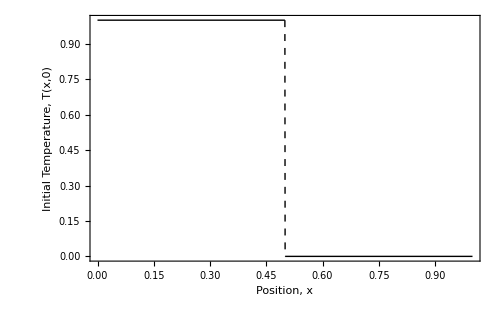

```mathematica
squareWavePlot=Plot[UnitStep[x(1/2-x)],{x,0,1},PlotStyle->Directive[Black,Thick],Frame->True,LabelStyle->Directive[Black,16],ImageSize->500,FrameLabel->{"Position, x","Initial Temperature, T(x,0)"},ExclusionsStyle->Dashed]
```

We can indeed model this using an appropriate Fourier Series

```mathematica
Manipulate[
DynamicModule[{fs,fcs,fss},
fs=FourierSeries[UnitStep[x(1/2-x)],x,n,FourierParameters->{1,2Pi}];
fcs=FourierCosSeries[UnitStep[x(1/2-x)],x,n,FourierParameters->{1,2Pi}];
fss=FourierSinSeries[UnitStep[x(1/2-x)],x,n,FourierParameters->{1,2Pi}];
Show[squareWavePlot,Plot[{fs,fcs,fss},{x,0,1},PlotStyle->{Red,Directive[RGBColor[0,1/3,0],Dashed],Directive[Blue,Dashed]}],PlotRange->5/4{-1,1}]],{{n,1,"Fourier Terms"},1,20,2},Paneled->False]
```

Notes:

Mathematica’s default convention for “Fourier Parameters” (which are just conventions for the formulas used) are slightly different than the ones we’re used to, so we explicitly specify them

```mathematica
?FourierParameters
```

We used three different Fourier Series expansions above

One using only Cosine terms `FourierCosSeries`, in Green

One using only Sine terms `FourierSinSeries`, in Blue

One using complex notation, `FourierSeries`, in Red

The accuracy of the approximation increases with more terms in the expansion

And indeed, if we let Mathematica turn its gears, we obtain a symbolic solution involving an infinite series of sine and cosine terms

```mathematica
heatSolution["unit-step"][m_][x_,t_]=DSolveValue[{heatEquation,heatBCs,heatIC[UnitStep[x(1/2-x)]]},T[x,t],{x,t}]/.∞->m
```

1/2+2 (ⅇ^(-π^2 t K[1]^2) Cos[π x K[1]] Sin[1/2 π K[1]])/(π K[1])K[1]1m

```mathematica
With[{f=Activate[heatSolution["unit-step"][100][x,t]]},
Plot3D[f,{x,0,1},{t,0,0.25},
PlotRange->All,MeshFunctions->{#2&},PlotStyle->None,Mesh->25,PlotPoints->25,
MeshStyle->Directive[Black,Thick],BoundaryStyle->Directive[Black,Thick],ImageSize->500,
AxesLabel->{"Position, x","Time, t","T(x,t)"},BaseStyle->Directive[16,Black],LabelStyle->Directive[16,Black]]]
```

-Graphics3D-

## ‘Fourier’ Epicycles

Let’s see how far we can push this idea of “approximating periodic curves” using sine and cosine terms

First, note that it’s more convenient to work in complex notation, using Euler’s formula

-Graphics-

Where the cosine and sine terms are given by:

-Graphics-

In addition to the sine-cosine relation to exponentials, the above figure further demonstrates the “polar” notation of complex numbers, which can be interpreted as counter-clockwise notations in the complex plane

To investigate this “polar” mapping, let’s imagine the curve traced by a particle on a wheel with unit radius

```mathematica
Manipulate[
ParametricPlot[{Cos[t],Sin[t]},{t,-10^-6,tmax},Frame->True,PlotStyle->Red,PlotRange->2{{-1,1},{-1,1}},LabelStyle->Directive[16,Black],ImageSize->250],{{tmax,0,"Extent of Trace"},0,2π},Paneled->False,SaveDefinitions->True]
```

And then add another wheel at the tip of this wheel, with half the radius, and rotating 7 times as fast

```mathematica
Manipulate[
ParametricPlot[{{Cos[t],Sin[t]},{Cos[tmax],Sin[tmax]}+1/2{Cos[7t],Sin[7t]},
{Cos[t],Sin[t]}+1/2{Cos[7t],Sin[7t]}},{t,-10^-6,tmax},Frame->True,PlotStyle->{Directive[Red,Dashed],Directive[Blue,Dashed],Blue},PlotRange->2{{-1,1},{-1,1}},LabelStyle->Directive[16,Black],ImageSize->250],{{tmax,0,"Extent of Trace"},0,2π},Paneled->False,SaveDefinitions->True]
```

And then add yet another one at the tip of the second wheel with a third of the radius, rotating 17 times as fast, in the opposite direction

```mathematica
Manipulate[
ParametricPlot[{
{Cos[t],Sin[t]},
{Cos[tmax],Sin[tmax]}+1/2{Cos[7t],Sin[7t]},
{Cos[tmax],Sin[tmax]}+1/2{Cos[7tmax],Sin[7tmax]}+1/3{Sin[17t],Cos[17t]},
{Cos[t],Sin[t]}+1/2{Cos[7t],Sin[7t]}+1/3{Sin[17t],Cos[17t]}},{t,-10^-6,tmax},Frame->True,PlotStyle->{Directive[Red,Dashed],Directive[Blue,Dashed],Directive[RGBColor[0,1/3,0],Dashed],RGBColor[0,1/3,0]},PlotRange->2{{-1,1},{-1,1}},LabelStyle->Directive[16,Black],ImageSize->250],{{tmax,0,"Extent of Trace"},0,2π},Paneled->False,SaveDefinitions->True]
```

And indeed, given enough little “wheels”, with varying radii, rotating at different rates, we can reproduce (almost) any closed periodic curve!

To see this, let’s express the final expression above in the complex plane

```mathematica
TrigToExp[#1+ⅈ#2&@@{Cos[t]+1/2 Cos[7 t]+1/3 Sin[17 t],1/3 Cos[17 t]+Sin[t]+1/2 Sin[7 t]}]
```

ⅇ^(ⅈ t)+1/2 ⅇ^(7 ⅈ t)+1/3 ⅈ ⅇ^(-17 ⅈ t)

and recognize we can generalize this as

where  is the radius of each wheel

rotating with a phase

at an angular velocity

We now wish to extract these coefficients c_i given a closed periodic list of complex points

E.g. this elephant shape

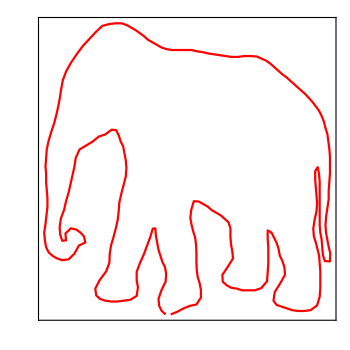

```mathematica
ListLinePlot[,Frame->True,PlotStyle->Red,ImageSize->350,AspectRatio->1,FrameTicks->None]
```

The operation to extract the coefficients c_j given a list of complex points is very similar to extracting the coefficients of a Discrete Fourier Transform (DFT)

but ever so slightly different, so let’s quickly write our own

```mathematica
fourierCoefficients[data_,frequencyRange_]:=With[{n=Length[data]},
1/n*Table[Sum[data[[k]]*Exp[-I i k 2 Pi/n],{k,1,n}],{i,-frequencyRange,frequencyRange}]]
```

We first need to map our (x,y) points to the complex plane

```mathematica
complexElephantPoints=#1+#2ⅈ &@@@;
```

and then extract our coefficients for the first 10 frequencies as

```mathematica
fourierCoefficients[complexElephantPoints,10]
```

{-2.08035-0.0732252 ⅈ,-10.6504-8.63105 ⅈ,-3.99168-11.6547 ⅈ,5.69277-0.747683 ⅈ,-13.1111+0.225971 ⅈ,5.44969+4.27748 ⅈ,24.9125-1.47412 ⅈ,-11.3133-24.8213 ⅈ,16.5102+49.9785 ⅈ,-38.2285-148.453 ⅈ,23.2813-101.483 ⅈ,-0.749964+46.7083 ⅈ,0.0884183-5.67611 ⅈ,-6.21188-9.24998 ⅈ,-14.1563-2.72538 ⅈ,-1.79597+6.42171 ⅈ,14.5257-0.225579 ⅈ,1.09041-5.63315 ⅈ,0.357429-15.4818 ⅈ,2.52331-5.03105 ⅈ,0.287394+4.0303 ⅈ}

We can then implement the formula above as

```mathematica
epicyclesRepresentation[coefficients_,frequencyRange_][t_]:=Sum[coefficients[[j]]Exp[ⅈ(j-frequencyRange-1)t],{j,1,2 frequencyRange+1}]
```

```mathematica
epicyclesRepresentation[fourierCoefficients[complexElephantPoints,10],10][t]
```

(23.2813-101.483 ⅈ)-(38.2285+148.453 ⅈ) ⅇ^(-ⅈ t)-(0.749964-46.7083 ⅈ) ⅇ^(ⅈ t)+(16.5102+49.9785 ⅈ) ⅇ^(-2 ⅈ t)+(0.0884183-5.67611 ⅈ) ⅇ^(2 ⅈ t)-(11.3133+24.8213 ⅈ) ⅇ^(-3 ⅈ t)-(6.21188+9.24998 ⅈ) ⅇ^(3 ⅈ t)+(24.9125-1.47412 ⅈ) ⅇ^(-4 ⅈ t)-(14.1563+2.72538 ⅈ) ⅇ^(4 ⅈ t)+(5.44969+4.27748 ⅈ) ⅇ^(-5 ⅈ t)-(1.79597-6.42171 ⅈ) ⅇ^(5 ⅈ t)-(13.1111-0.225971 ⅈ) ⅇ^(-6 ⅈ t)+(14.5257-0.225579 ⅈ) ⅇ^(6 ⅈ t)+(5.69277-0.747683 ⅈ) ⅇ^(-7 ⅈ t)+(1.09041-5.63315 ⅈ) ⅇ^(7 ⅈ t)-(3.99168+11.6547 ⅈ) ⅇ^(-8 ⅈ t)+(0.357429-15.4818 ⅈ) ⅇ^(8 ⅈ t)-(10.6504+8.63105 ⅈ) ⅇ^(-9 ⅈ t)+(2.52331-5.03105 ⅈ) ⅇ^(9 ⅈ t)-(2.08035+0.0732252 ⅈ) ⅇ^(-10 ⅈ t)+(0.287394+4.0303 ⅈ) ⅇ^(10 ⅈ t)

and finally convert back to (x,y) and plot

```mathematica
parametricEquationsEpicycles[data_,frequencyRange_]:=Block[{coefficients,representation},
coefficients=fourierCoefficients[data,frequencyRange];
representation=epicyclesRepresentation[coefficients,frequencyRange][t];
Function[t,Evaluate[ReIm[ComplexExpand[representation]]]]
]
```

```mathematica
Manipulate[
With[{f=parametricEquationsEpicycles[complexElephantPoints,n]},
ParametricPlot[f[t],{t,0,2π},Axes->False,PlotStyle->Red,ImageSize->350,AspectRatio->1]],{{n,10,"Numbe of Terms"},5,100,5},Paneled->False]
```

We can also visualize the individual epicycles

```mathematica
epicyclesVisualization[data_,frequencyRange_]:=Block[{coefficients,radii,phase,ordering,edgePoints,circles},
coefficients=fourierCoefficients[data,frequencyRange];
radii=Abs/@coefficients;
phase=Arg/@coefficients;
ordering={frequencyRange+1}~Join~Riffle[Range[frequencyRange+2,2 frequencyRange+1],Reverse[Range[1,frequencyRange]]];

edgePoints[t_]=
ReIm[Accumulate[Table[coefficients[[j]]Exp[ⅈ(j-frequencyRange-1)t],{j,ordering}]]];
circles[t_]=Table[Circle[edgePoints[t][[j-1]],radii[[ordering[[j]]]]],{j,2,2frequencyRange+1}];

Function[t,Evaluate[{circles[t],Line[edgePoints[t]],Point[edgePoints[t]]}]]

]
```

```mathematica
Manipulate[
With[{
f=parametricEquationsEpicycles[complexElephantPoints,n],
gr=epicyclesVisualization[complexElephantPoints,n]},
Animate[
ParametricPlot[f[s],{s,-10^-6,t},PlotStyle->Red,AspectRatio->Automatic,Axes->False,Epilog->gr[t],PlotRange->{{-400,400},{-400,200}},ImageSize->500],{{t,0,"Time"},0,2π},AnimationRunning->False,AnimationRate->.1,Paneled->False]],{{n,10,"Numbe of Terms"},5,100,5},Paneled->False]
```

The “person-curves” in Mathematica are built using a similar way

```mathematica
EntityList[EntityClass["PopularCurve","Person"]]
```